# Atomic Orbitals

Electron: Wave or Particle?

Rishab Nayak, Jun. 24,  2018

As described by quantum mechanics, an atomic orbital is a mathematical function describing the wave-like behavior of an electron or a pair of electrons in an atom. The probability of finding an electron in a specific region around an atom can be calculated by the function of the atomic orbital.

Each orbital has a unique shape, as described by a unique set of three quantum numbers - n, l, and m, each corresponding respectively to the energy of the electron, its angular momentum and the vector component of the angular momentum (the magnetic quantum number). Each orbital thus described can be occupied by a maximum of two electrons, each with its spin quantum number s.

The names s, p, d and f orbitals refer to orbitals with angular momentum quantum number l = 0, 1, 2 and 3 respectively. Atomic orbitals are primitives for the atomic orbital model, which is more commonly known as the wave mechanics model. The orbitals signify discrete energy levels, which is also observed in the atomic spectra of elements.

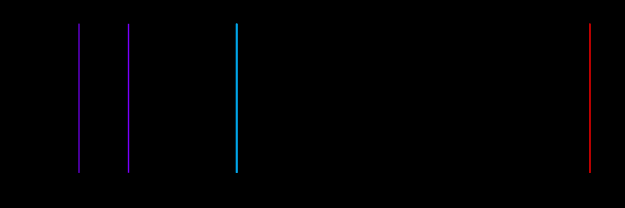

```mathematica
linesh = SpectralLineData[EntityClass["AtomicLine",{"Hydrogen",1}],{Quantity[400,"nm"],Quantity[750, "nm"]}];
linevaluesh=QuantityMagnitude[SpectralLineData[linesh,"Wavelength"],"Nanometers"];
Graphics[{ColorData["VisibleSpectrum"][#],Line[{{#,0},{#,1}}]}&/@linevaluesh,Frame->True,FrameTicks->{True,False},AspectRatio->1/3,Background->Black,FrameLabel->Quantity[None,"Nanometers"],PlotLabel->"Spectral Emission Data for Hydrogen"]
```

This clearly shows that atoms emit and absorb light at a discrete set of frequencies characteristic to the element, serving as proof to the presence of atomic orbitals, and their uniqueness.

## A Simple Model: The Hydrogen Atom

The hydrogen atom is the most elementary example of a single electron atom, other single electron ions could include He^+,Li^(2+)and other ions in which all but one electron have been stripped off. All these only differ in charge +Ze on the nucleus. The potential energy for the hydrogen atom, in the context of the Bohr model depends only on the distance of the electron from the nucleus.

The solution for the Schrödinger equation for the atom defines the distribution of the electron density around it. Since the atom has to exist in 3D space, the coordinates for the electron distribution are better defined in spherical coordinates, rather than Cartesian space. The solution must also be continuous in all three coordinates.

Energy levels need to be quantized, as per the physical boundary conditions (Ψ → 0, and r→ ∞) imposed on the Schrödinger equation.

“n” refers to the principal quantum number indexes the individual energy levels

“l” refers to the angular momentum quantum number, and can take on integral values from 0 to n-1

“m” refers to the magnetic quantum number and can take on integral values from -l to l

For each quantum state (n, l, m), the solution of the Schrödinger equation provides a wave function of the form:

Ψ_nlm(r,θ,ϕ) = R_nl(r)Y_lm(θ,ϕ)

Where,

“r” refers to the distance of the electron from the nucleus

θ is related to the latitude

ϕ is related to the longitude

The wavefunction for the atom (ϕ_nlm(r,θ,ϕ) in the state (n, l, m) is called an orbital. These orbitals bear no real resemblance to the circular orbits of the Bohr atom. These orbitals precisely describe the probability density of finding the electron at a point.

## Orbitals

### s Orbitals

These correspond to Ψ_nlm with l=0, which means m=0. For all s orbitals, the angular part is constant, thus making the s orbitals spherically symmetric.

```mathematica
SphericalPlot3D[Evaluate[Re(Subscript[Y, 1]^1(θ,ϕ))],{θ,0,π},{ϕ,0,2π}]
```

-Graphics3D-

Nodes refer to points with zero electron probability density. s orbitals have radial nodes only, present starting from n = 2, the formula for the number of nodes being n-1.

### p Orbitals

These correspond to Ψ_nlm with l=1, which means -1<m<1. All p orbitals are dumbbell shaped, having a node in the middle.

```mathematica
Row[{SphericalPlot3D[Re[SphericalHarmonicY[1,-1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[1,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[1,1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}]}]
```

-Graphics3D--Graphics3D--Graphics3D-

p orbitals have both radial and angular nodes. The number of angular nodes is l, and the number of radial nodes is n-l-1.

d Orbitals

These correspond to Ψ_nlm with l=2, which means -2<m<2. d orbitals have complex shapes, some double dumbbell.

```mathematica
Row[{SphericalPlot3D[Re[SphericalHarmonicY[2,-2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[2,-1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[2,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[2,1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[2,2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}]}]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

d orbitals have both radial and angular nodes. The number of angular nodes is l, and the number of radial nodes is n-l-1.

f Orbitals

These correspond to Ψ_nlm with l=3, which means -3<m<3. f orbitals have complex shapes.

```mathematica
Row[{SphericalPlot3D[Re[SphericalHarmonicY[3,-3,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[3,-2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[3,-1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[3,0,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],SphericalPlot3D[Re[SphericalHarmonicY[3,1,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],
SphericalPlot3D[Re[SphericalHarmonicY[3,2,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}],
SphericalPlot3D[Re[SphericalHarmonicY[3,3,θ,ϕ]]^2,{θ,0,π},{ϕ,0,2 π}]}]
```

-Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D--Graphics3D-

## Further Explorations

Hartree Orbitals

Linear Combination of Atomic Orbitals

Orbital Hybridization

## Author contact information

rishab@bu.edu